{10,20,40,80,160,320,640,1280,2560,5120,10240,20480,40960,81920,163840,327680,655360,1310720,2621440}

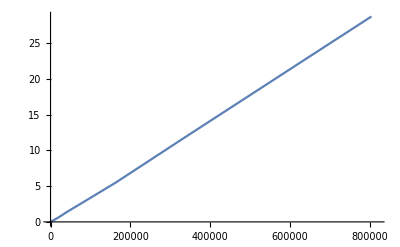

```mathematica
(*ins={25,55,130,290,610,1402,3002,6253,13933,29293,60661,132341,275701,565843,1221203,2531923,5153363,11042384,22838864}*)
ins=Table[2^x 10,{x,0,18}]
outs={0.00,0.00,0.00,0.01,0.01,0.01,0.02,0.04,0.08,0.18,0.32,0.64,1.39,2.76,5.52,11.51,23.38,47.08,101.12};
len=Length[ins];
pairs=Table[{ins[[i]],outs[[i]]},{i,1,len}];
ListPlot[pairs,Joined->True]
```

-0.283422+0.0000380431 x

0.00932795+0.0000338552 x+1.78925×10^-12 x^2

-0.0327879+0.0000353501 x-2.55287×10^-13 x^2+5.68112×10^-19 x^3

-0.00489602+0.0000332581 x+6.61623×10^-12 x^2-5.24539×10^-18 x^3+1.33338×10^-24 x^4

0.00270749+0.0000321358 x+1.46083×10^-11 x^2-2.11268×10^-17 x^3+1.22982×10^-23 x^4-2.29164×10^-30 x^5

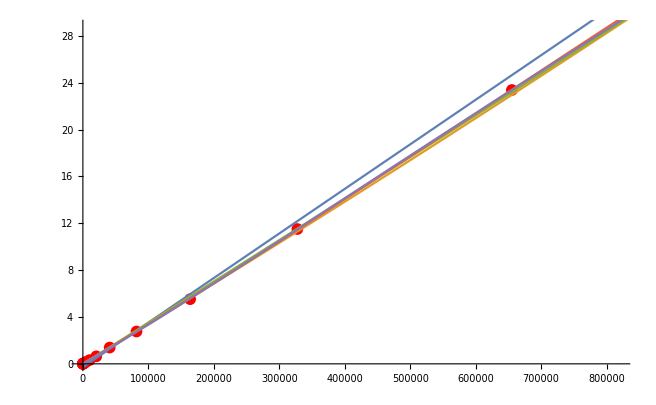

```mathematica
data=pairs;
line = Fit[data, {1,x},x]
parabola = Fit[data, {1,x,x^2}, x]
cubic = Fit[data, {1,x,x^2,x^3}, x]
quartic = Fit[data, {1,x,x^2,x^3,x^4}, x]
quintic = Fit[data, {1,x,x^2,x^3,x^4,x^5}, x]
Show[ListPlot[data, PlotStyle->Red], Plot[{line, parabola,cubic,quartic,quintic}, {x, 0,Max[ins]}]]
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[-0.283422+0.0000380431 x]

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 11167. | 11167. | 15595.1 | 1.24437×10^-26
Error | 17 | 12.173 | 0.716061 |  | 
Total | 18 | 11179.2 |  |  |

```mathematica
10*2^18
```

2621440

```mathematica
ScientificForm[0.0000380431]
```

3.80431×10^-5

```mathematica
ConstantArray[1,2]
```

{1,1}

```mathematica
Flatten[Map[rep,FactorInteger[6]]]
Map[PrimePi,%]
```

{2,3}

{1,2}

```mathematica
facs[x_]:=Flatten[Map[rep,FactorInteger[x]]]
```

```mathematica
rep[{a_,b_}]:=ConstantArray[a,b]
```

```mathematica
pinv[x_]:=Piecewise[{{1, x==1}, {Map[pinv,facs[PrimePi[x]]], PrimeQ[x]}, {Map[pinv,facs[x]], True}}]
```

```mathematica
pinv[2]
```

{1}

```mathematica
pinv[3]
```

{{1}}

```mathematica
pinv[4]
```

{{1},{1}}

```mathematica
pinv[7]
```

{{1},{1}}

```mathematica
Table[pinv[i],{i,1,10}]
```

{1,{{1}},{{{{1}}}},{{{1}},{{1}}},{{{{{{1}}}}}},{{{1}},{{{{1}}}}},{{{{1}},{{1}}}},{{{1}},{{1}},{{1}}},{{{{{1}}}},{{{{1}}}}},{{{1}},{{{{{{1}}}}}}}}

```mathematica
{
1,1
{1},2
{{1}},3
{{1},{1}},5
{{{1}}},4
{{1},{{1}}},5
{{1},{1}},
{{1},{1},{1}},
{{{1}},{{1}}},
{{1},{{{1}}}}
}
```

```mathematica
numv[l_]:=If[!ListQ[l],1,
1+Total[Map[numv,l]]]
```

```mathematica
Monitor[Table[numv[pinv[i]],{i,1,10}],i]
```

{1,2,3,5,4,6,5,7,7,7}

```mathematica
enumTails[x_,max_]:=Table[
If[ListQ[x[[j,2]]],Join[{x[[j,1]]->(max+j)},Map[(max+j)->#&,x[[j,2]]]],
{x[[j,1]]->(max+j)}]
,{j,1,Length[x]}]
```

```mathematica
ittree[l_]:=Block[{done=Select[l,!(ListQ[#[[2]]]||(#[[1]]≠0&&#[[2]]==1))&],notdone=Select[l,(ListQ[#[[2]]]||(#[[1]]≠0&&#[[2]]==1))&],max=Max[Flatten[Map[{#[[1]],#[[2]]}&,l]]]},
Join[Flatten[enumTails[notdone,max],1],done]]
```

{0->2,2->1,0->3,3->{{1}},3->{1},0->4,4->{1}}

{2->5,3->6,6->{1},3->7,7->1,4->8,8->1,0->2,0->3,0->4}

{6->9,9->1,7->10,8->11,2->5,3->6,3->7,4->8,0->2,0->3,0->4}

{9->12,6->9,7->10,8->11,2->5,3->6,3->7,4->8,0->2,0->3,0->4}

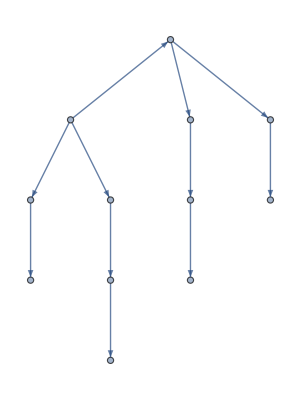

```mathematica
ittree[l1]
ittree[%]
ittree[%]
ittree[%]
Graph[%]
```

```mathematica
ftree[x_]:=Graph[NestWhile[ittree,Table[0->x[[j]],{j,1,Length[x]}],Or@@Map[If[ListQ[Last[#]],True,(#[[1]]≠0)&&(#[[2]]==1)]&,#]&]]
```

```mathematica
ftree[{{1},{{{1}},{1}},{{1}}}]
```

-Graphics-

```mathematica
pinv[4]
```

{{1},{1}}

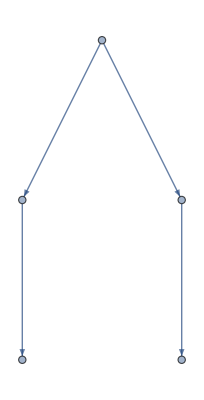

```mathematica
ftree[{{1},{1}}]
```

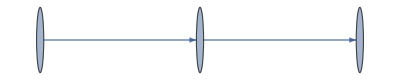
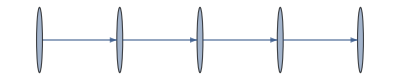
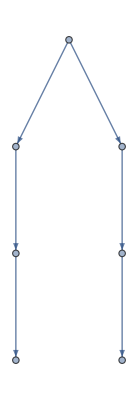
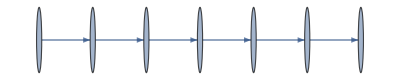
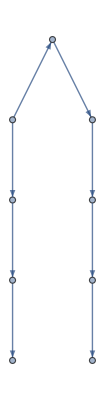
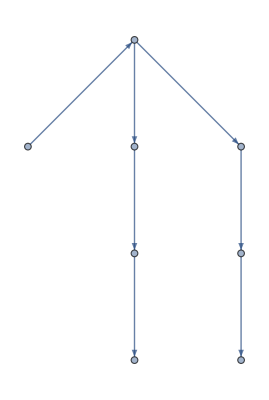
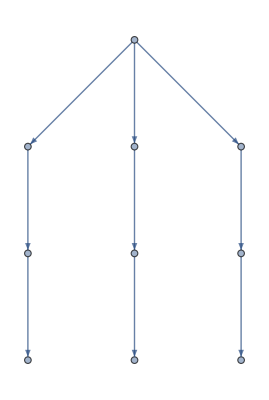
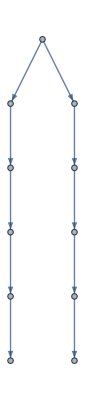
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ftree[pinv[i]],{i,1,9}]
```

```mathematica
pinv[4]
```

{{1},{1}}

```mathematica
pinv[7]
```

{{1},{1}}